This Mathematica code is part of the lecture script Introduction to Computational Quantum Mechanics by Roman Schmied. It is licensed under a Creative Commons Attribution-ShareAlike 4.0 International License.

-Graphics-

You can download the associated lecture script at http://arxiv.org/abs/1403.7050

# Quantum Gates and Quantum Computing

-Graphics-

## definitions of quantum gates

## single - qubit

### single-qubit pseudospin operators: 𝟙, (σ̂)_x, (σ̂)_y, (σ̂)_z

-Graphics-

```mathematica
{id,σx,σy,σz}=Table[SparseArray[PauliMatrix[i]],{i,0,3}];
```

### projectors onto 0 and 1 states, respectively:

```mathematica
P0=(id+σz)/2//SparseArray;
P1=(id-σz)/2//SparseArray;
```

### phase shift gate

-Graphics-

-Graphics-

-Graphics-

### Hadamard gate:

-Graphics-

```mathematica
H[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,(σx+σz)/(√2)]
Hadamand = H[1,1] ;
%// Normal // MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

## n - qubit gates

### operator â acting on the k^th qubit of a set of n qubits: 𝟙⊗𝟙⊗⋯⊗𝟙⊗â⊗1⊗⋯⊗𝟙⊗𝟙

```mathematica
op[n_Integer,k_Integer,a_]/;1≤k≤n∧Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]]
```

```mathematica
op[1,1,Hadamand];
%// Normal // MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

### single-qubit gates acting on the k^th qubit of a set of n qubits

Pauli gates acting on the k^th qubit of a set of n qubits:

```mathematica
X[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σx]
Y[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σy]
Z[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,σz]
```

### Pauli rotations: (R̂)_x(ϕ)∝ⅇ^(-ⅈ ϕ (σ̂)_x/2) etc.

```mathematica
RX[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σx]
RY[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σy]
RZ[n_Integer,k_Integer,ϕ_]/;1≤k≤n:=op[n,k,(1+ⅇ^(ⅈ ϕ))/2 id+(1-ⅇ^(ⅈ ϕ))/2 σz]
RX[1,1,Pi];
% // Normal //MatrixForm
```

(0 | 1
1 | 0)

```mathematica
RY[1,1,Pi];
% // Normal //MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
RZ[1,1,Pi];
% // Normal //MatrixForm
```

(1 | 0
0 | -1)

### controlled operator

controlled operator: in a set of n qubits, only if all of the qubits in the list λ are in state 1 then the operator Â is applied to the system; otherwise no operation is applied

-Graphics-

-Graphics-

```mathematica
CTRL[n_Integer,λ_/;VectorQ[λ,IntegerQ],A_]/;(Unequal@@λ)∧Min[λ]≥1∧Max[λ]≤n∧Dimensions[A]=={2^n,2^n}:=IdentityMatrix[2^n,SparseArray]+Apply[Dot,op[n,#,P1]&/@λ].(A-IdentityMatrix[2^n,SparseArray]
```

## two-qubit gates

### SWAP gate: exchanges the state of qubits j and k in a set of n qubits

-Graphics-

```mathematica
SWAP[n_Integer,{j_Integer,k_Integer}]/;1≤j≤n∧1≤k≤n∧j≠k:=(IdentityMatrix[2^n,SparseArray]+X[n,j].X[n,k]+Y[n,j].Y[n,k]+Z[n,j].Z[n,k])/2
SWAP[3,{2,1}]//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### square root of the SWAP gate:

-Graphics-

```mathematica
SQRTSWAP[n_Integer,{j_Integer,k_Integer}]/;1≤j≤n∧1≤k≤n∧j≠k:=(3+ⅈ)/4 IdentityMatrix[2^n,SparseArray]+(1-ⅈ)/4(X[n,j].X[n,k]+Y[n,j].Y[n,k]+Z[n,j].Z[n,k])
```

```mathematica
SQRTSWAP[3,{2,3}]//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### CNOT gate

CNOT gate: in a set of n qubits, if qubit j is in state 0 then there is no effect on qubit k, whereas if qubit j is in state 1 then the NOT operator (σ̂)_x acts on qubit k

-Graphics-

```mathematica
CNOT[n_Integer,j_Integer->k_Integer]/;1≤j≤n∧1≤k≤n∧j≠k:=CTRL[n,{j},op[n,k,σx]]
CNOT[3,3,2] //Normal // MatrixForm
```

CNOT[3,3,2]

### controlled phase shift

-Graphics-

-Graphics-

## three-qubit gates

### CCNOT

CCNOT (Toffoli) gate: in a set of n qubits, if both qubits i and j are in state 1, then the NOT operator (σ̂)_x acts on qubit k

```mathematica
CCNOT[n_Integer,{i_Integer,j_Integer}->k_Integer]/;1≤i≤n∧1≤j≤n∧1≤k≤n∧Unequal[i,j,k]:=CTRL[n,{i,j},op[n,k,σx]]
CCNOT[3,{3,2}->1]//Normal//MatrixForm
```

CTRL[3,{3,2},{{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}}]

### controlled SWAP

controlled SWAP (Fredkin) gate: in a set of n qubits, if qubit i is in state 0 then there is no effect on qubits j and k, whereas if qubit i is in state 1 then the state of qubits j and k is exchanged

```mathematica
CSWAP[n_Integer,i_Integer->{j_Integer,k_Integer}]/;1≤i≤n∧1≤j≤n∧1≤k≤n∧Unequal[i,j,k]:=CTRL[n,{i},SWAP[n,{j,k}]]
CSWAP[3,2->{1,3}]//Normal//MatrixForm
```

CTRL[3,{2},{{1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1}}]

## a simple circuit

-Graphics-

-Graphics-

### the operator for the circuit:

```mathematica
S=CNOT[2,1->2].H[2,1];
Normal[S]
```

CTRL[2,{1},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}].{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{1/(√2),0,-1/(√2),0},{0,1/(√2),0,-1/(√2)}}

### the basis set:

```mathematica
B[n_Integer/;n≥1]:=Tuples[{0,1},n]
B[2]
```

{{0,0},{0,1},{1,0},{1,1}}

### operate on the 00 input state:

```mathematica
ψin={1,0,0,0};
ψout=S.ψin
```

CTRL[2,{1},SparseArray[…]].{1/(√2),0,1/(√2),0}

```mathematica
CTRL[2,{1},SparseArray[…]].{1/(√2),0,1/(√2),0}//Normal//MatrixForm;
```

### measurement

-Graphics-

-Graphics-

### note

-Graphics-

## Teleportation algorithm

In outline, the steps of the solution are as follows : Alice interacts the qubit | ψ⟩ with her half of the EPR pair, and then measures the two qubits in her possession, obtaining one of four possible classical results, 00, 01, 10, and 11. She sends this information to Bob.Depending on Alice' s classical message, Bob performs one of four operations on his half of the EPR pair.By doing this he can recover the original state | ψ⟩

The quantum circuit shown in Figure 1.13 gives a more precise description of quantum teleportation.The state to be teleported is | ψ⟩ = α | 0 ⟩ + β | 1 ⟩, where α and β are unknown amplitudes.The state input into the circuit | ψ0 ⟩ is | ψ0 ⟩ = | ψ⟩ | β00 ⟩

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
B[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
ψin1=1/2^(1/2){α,0,0,α,β,0,0,β};
```

```mathematica
Sum[ψin1[[i]]ket[B[3][[i]]],{i,Length[ψin1]}]
```

(α ket[{0,0,0}])/(√2)+(α ket[{0,1,1}])/(√2)+(β ket[{1,0,0}])/(√2)+(β ket[{1,1,1}])/(√2)

## Quantum Fourier Transform

The Quantum Fourier Transform (QFT) is assembled following Fig. 5.1 of M. Nielsen and I. Chuang, Quantum Computation and Quantum Information, Cambridge University Press, 2010 (tenth anniversary edition).

The quantum circuit for a QFT is assembled from blocks that connect the i^th qubit to the qubits {i+1,i+2,…,n} via controlled phase gates:

-Graphics-

```mathematica
QFTblock[n_Integer,i_Integer]/;1≤i≤n:=Apply[Dot,Table[CTRL[n,{j},RZ[n,i,2π/2^(j+1-i)]],{j,n,i+1,-1}]].H[n,i]
```

assemble the quantum Fourier transformation by connecting all qubits:
1. connect all qubits through the above QFTblock operation
2. swap the order of the qubits

```mathematica
QFT[n_Integer]/;n≥1:=Apply[Dot,Table[SWAP[n,{i,n+1-i}],{i,1,n/2}]].Apply[Dot,Table[QFTblock[n,i],{i,n,1,-1}]]
```

QFT consists of a polynomial number of gates:
· n Hadamard gates
· (n(n-1))/2 controlled rotations
· ⌊n/2⌋ swap gates

simple formula for the resulting matrix representation:

```mathematica
Table[QFT[n]==1/2^(n/2)Table[ⅇ^(2π ⅈ j k/2^n),{j,0,2^n-1},{k,0,2^n-1}],{n,6}]//FullSimplify
```

{True,1=={1},2,1,1=={{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},62,{1/8,-1/8 (-1)^(31/32),-1/8 (-1)^(15/16),-1/8 (-1)^(29/32),-1/8 (-1)^(7/8),-1/8 (-1)^(27/32),52,1/8 (-1)^(3/16),1/8 (-1)^(5/32),1/8 (-1)^(1/8),1/8 (-1)^(3/32),1/8 (-1)^(1/16),1/8 (-1)^(1/32)}}}
 |  |  |  |

## Quantum phase estimation

given a unitary operator Uˆφ and an eigenstate | u⟩ such that Uˆφ | u⟩ = e2πiφ | u⟩, can we estimate φ efficiently, that is, to t binary digits with an effort that scales polynomially with t?

-Graphics-

estimate the phase of this:

```mathematica
u={1};
U[ϕ_]={{ⅇ^(2π ⅈ ϕ)}};
```

check that we set up the problem correctly:

```mathematica
{U[ϕ].u===ⅇ^(2π ⅈ ϕ)u,Norm[u]==1}
```

{True,True}

unit operator in the space of the system U:

```mathematica
U0=IdentityMatrix[Length[u],SparseArray];
```

U operator attached to n qubits, controlled by the i^th qubit:

```mathematica
CTRLU[n_Integer,i_Integer,ϕ_]/;1≤i≤n:=KroneckerProduct[op[n,i,P0],U0]+KroneckerProduct[op[n,i,P1],U[ϕ]]
```

estimate to t digits of precision:

```mathematica
t=4;
ϵ[ϕ_]=KroneckerProduct[ConjugateTranspose[QFT[t]],U0].Apply[Dot,Table[CTRLU[t,i,2^(t-i)ϕ],{i,t,1,-1}]].KroneckerProduct[Apply[Dot,Table[H[t,i],{i,t}]],U0].Flatten[KroneckerProduct[SparseArray[1->1,2^t],u]]//Normal;
```

probabilities for measuring the different basis states: trace out the SUT and look at the diagonal elements of the reduced density matrix
(see ReducedDensityMatrix.nb)

```mathematica
rdm[ψABC_?VectorQ,{dA_Integer/;dA≥1,dB_Integer/;dB≥1,dC_Integer/;dC≥1}]/;Length[ψABC]==dA dB dC:=
With[{P=ArrayReshape[ψABC,{dA,dB,dC}]},
Flatten[Transpose[P,{1,3,2}].ConjugateTranspose[P],{{1,2},{3,4}}]]
traceout[ψ_?VectorQ,d_Integer/;d≥1]/;Divisible[Length[ψ],d]:=rdm[ψ,{1,d,Length[ψ]/d}]
traceout[ψ_?VectorQ,d_Integer/;d≤-1]/;Divisible[Length[ψ],-d]:=rdm[ψ,{Length[ψ]/-d,-d,1}]
```

```mathematica
prob[ϕ_?NumericQ]:=Re[Diagonal[traceout[ϵ[N[ϕ]],-Length[u]]]]
```

When ϕ is an integer multiple of 2^-t, only one basis state has 100% probability of occurring. The i^th basis state corresponds to a measurement of ϕ=(i-1)/2^t:

```mathematica
Table[prob[ϕ],{ϕ,0,1,2^-t}]//Chop//MatrixForm
```

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.25+0. ⅈ},-1]].

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.23097+0.0956709 ⅈ,0.176777+0.176777 ⅈ,0.0956709+0.23097 ⅈ,«8»,-4.59243×10^-17-0.25 ⅈ,0.0956709-0.23097 ⅈ,0.176777-0.176777 ⅈ,0.23097-0.0956709 ⅈ},-1]].

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.176777+0.176777 ⅈ,1.53081×10^-17+0.25 ⅈ,-0.176777+0.176777 ⅈ,-0.25+3.06162×10^-17 ⅈ,«6»,-0.176777+0.176777 ⅈ,-0.25+9.18485×10^-17 ⅈ,-0.176777-0.176777 ⅈ,-1.07157×10^-16-0.25 ⅈ,0.176777-0.176777 ⅈ},-1]].

General::stop: Further output of Diagonal::list will be suppressed during this calculation.

(1)
 |  |  |  |

When ϕ is not an integer multiple of 2^-t, all basis states can occur in measurement:

```mathematica
Round[prob[0.2],0.001]
```

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.0772542+0.237764 ⅈ,-0.202254+0.146946 ⅈ,-0.202254-0.146946 ⅈ,0.0772542-0.237764 ⅈ,«7»,-0.202254+0.146946 ⅈ,-0.202254-0.146946 ⅈ,0.0772542-0.237764 ⅈ,0.25-1.83697×10^-16 ⅈ},-1]].

Round[Re[Diagonal[traceout[KroneckerProduct[ConjugateTranspose[{{1/(√2),1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(√2),1/(√2),0,0,0,0,0,0},{0,0,0,0,1/(√2),1/(√2),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),1/(√2),0,0},{0,0,1/(√2),1/(√2),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/(√2),1/(√2),0,0,0,0},{0,0,0,0,0,0,1/(√2),1/(√2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),1/(√2)},{1/(√2),-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(√2),-1/(√2),0,0,0,0,0,0},{0,0,0,0,1/(√2),-1/(√2),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),-1/(√2),0,0},{0,0,1/(√2),-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/(√2),-1/(√2),0,0,0,0},{0,0,0,0,0,0,1/(√2),-1/(√2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),-1/(√2)}}.CTRL[4,{4},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ}}].{{1/(√2),0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/(√2),0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0},{1/(√2),0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/(√2),0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/(√2),0,1/(√2),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/(√2),0,1/(√2),0,0,0,0,0,0,0,0},{0,0,0,0,1/(√2),0,-1/(√2),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/(√2),0,-1/(√2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(√2),0,1/(√2),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/(√2),0,1/(√2),0,0,0,0},{0,0,0,0,0,0,0,0,1/(√2),0,-1/(√2),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/(√2),0,-1/(√2),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,1/(√2),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,1/(√2)},{0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,-1/(√2),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,-1/(√2)}}.CTRL[4,{4},{{1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4))}}].CTRL[4,{3},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ}}].{{1/(√2),0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0},{0,1/(√2),0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0},{0,0,1/(√2),0,0,0,1/(√2),0,0,0,0,0,0,0,0,0},{0,0,0,1/(√2),0,0,0,1/(√2),0,0,0,0,0,0,0,0},{1/(√2),0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0},{0,1/(√2),0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0},{0,0,1/(√2),0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0},{0,0,0,1/(√2),0,0,0,-1/(√2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(√2),0,0,0,1/(√2),0,0,0},{0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,1/(√2),0,0},{0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,1/(√2),0},{0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,1/(√2)},{0,0,0,0,0,0,0,0,1/(√2),0,0,0,-1/(√2),0,0,0},{0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,-1/(√2),0,0},{0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,-1/(√2),0},{0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,-1/(√2)}}.CTRL[4,{4},{{1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8)),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/8))+1/2 (1+ⅇ^((ⅈ π)/8))}}].CTRL[4,{3},{{1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2 (1-ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4)),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1+ⅇ^((ⅈ π)/4))+1/2 (1+ⅇ^((ⅈ π)/4))}}].CTRL[4,{2},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ}}].{{1/(√2),0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0},{0,1/(√2),0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0},{0,0,1/(√2),0,0,0,0,0,0,0,1/(√2),0,0,0,0,0},{0,0,0,1/(√2),0,0,0,0,0,0,0,1/(√2),0,0,0,0},{0,0,0,0,1/(√2),0,0,0,0,0,0,0,1/(√2),0,0,0},{0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,1/(√2),0,0},{0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,1/(√2),0},{0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,1/(√2)},{1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0,0},{0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0},{0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0},{0,0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0,0,0},{0,0,0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0,0},{0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0,0},{0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2),0},{0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,-1/(√2)}}],{{1}}].{1/4,0.0772542+0.237764 ⅈ,-0.202254+0.146946 ⅈ,-0.202254-0.146946 ⅈ,0.0772542-0.237764 ⅈ,0.25-6.12323×10^-17 ⅈ,0.0772542+0.237764 ⅈ,-0.202254+0.146946 ⅈ,-0.202254-0.146946 ⅈ,0.0772542-0.237764 ⅈ,0.25-1.22465×10^-16 ⅈ,0.0772542+0.237764 ⅈ,-0.202254+0.146946 ⅈ,-0.202254-0.146946 ⅈ,0.0772542-0.237764 ⅈ,0.25-1.83697×10^-16 ⅈ},-1]]],0.001]

The mean measurement is a bad estimator (doesn’t converge as t→∞).
The most likely measurement is a good estimator.

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.25+0.0000320891 ⅈ,0.25+0.0000641782 ⅈ,0.25+0.0000962674 ⅈ,«8»,0.25+0.000385069 ⅈ,0.25+0.000417158 ⅈ,0.25+0.000449248 ⅈ,0.25+0.000481337 ⅈ},-1]].

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1.}}].{0.25,0.25+0.0000320891 ⅈ,0.25+0.0000641782 ⅈ,0.25+0.0000962674 ⅈ,«8»,0.25+0.000385069 ⅈ,0.25+0.000417158 ⅈ,0.25+0.000449248 ⅈ,0.25+0.000481337 ⅈ},-1.]].

Diagonal::list: List expected at position 1 in Diagonal[traceout[KroneckerProduct[ConjugateTranspose[«1»],{{1}}].{1/4,0.247943+0.0320011 ⅈ,0.241807+0.0634757 ⅈ,0.231693+0.093906 ⅈ,«8»,0.00762801+0.249884 ⅈ,-0.024421+0.248804 ⅈ,-0.0560681+0.243632 ⅈ,-0.0867928+0.23445 ⅈ},-1]].

General::stop: Further output of Diagonal::list will be suppressed during this calculation.

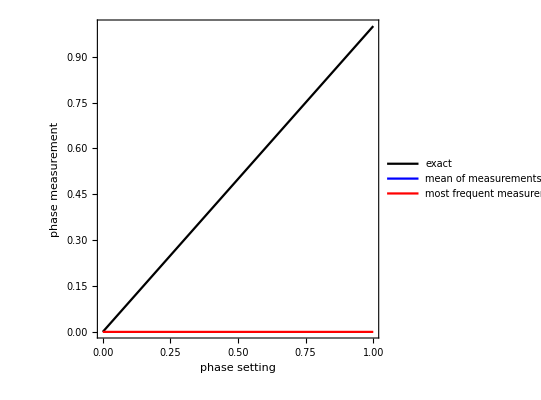

```mathematica
mean[ϕ_?NumericQ]:=prob[ϕ].(Range[0,2^t-1]/2^t);
mostprobable[ϕ_?NumericQ]:=(Ordering[prob[ϕ],-1]⟦1⟧-1)/2^t;
Plot[{ϕ,mean[ϕ],mostprobable[ϕ]},{ϕ,0,1},FrameLabel->{"phase setting","phase measurement"},LabelStyle->Directive[16,Black,Bold],PlotRange->{{0,1},{0,1}},PlotRangePadding->None,PlotStyle->{Black,{Thick,Blue},{Thick,Red}},AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"exact","mean of measurements","most frequent measurement"},GridLines->{Range[1,2^t-1]/2^t,Range[1,2^t-1]/2^t}]
```